```mathematica
Get["/Users/salehfh/Downloads/MFGraphs-master/MFGraphs/NonLinearSolver.m"]
```

```mathematica
alpha=1
```

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

```mathematica
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}];(crit=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

Iterative DNF convertion took 0.018692 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.030866,Null}

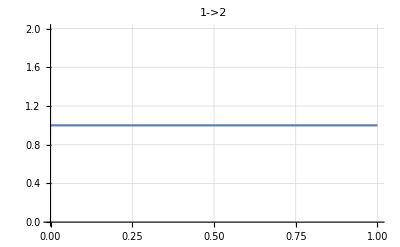
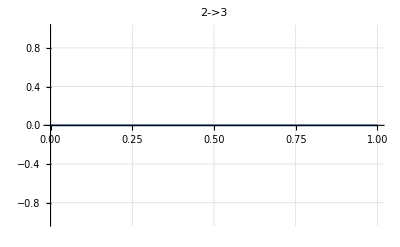
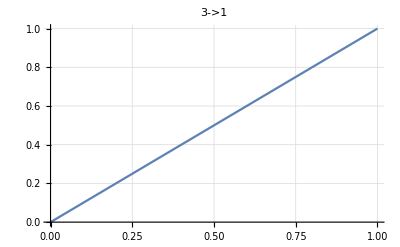

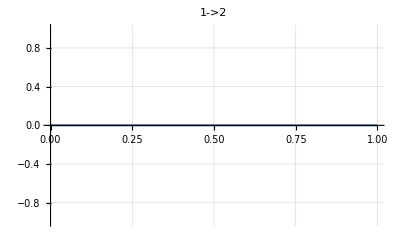
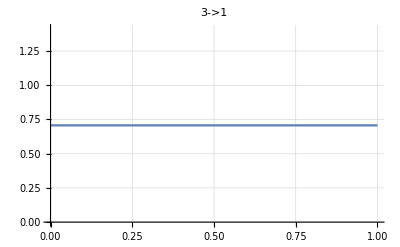
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotUs[crit,"AssoCritical"]
plotMs[crit,"AssoCritical"]
```

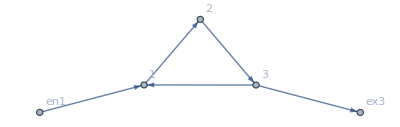

```mathematica
crit["FG"]
```

```mathematica
IsNonLinearSolution[crit][crit["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,1.11022×10^-15}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 1.11022×10^-15

<|u1→1.,u2→1.,u3→0.,u4→0.,u5→0.,u6→1.,u7→0.,u8→0.,u9→1.,u10→1.,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

```mathematica
alpha=1.2
```

Iterative DNF convertion took 0.018639 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,0.}
{0,0,-0.159104}

Iterative DNF convertion took 0.020132 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,-0.159104}
{0,0,-0.159104}

Iterative DNF convertion took 0.019014 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,-0.159104}
{0,0,-0.159104}

Iterated 3 times out of 15

{0.103374,Null}

All restrictions are True

Nlhs: {0.,0.,-0.159104}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,-0.159104}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 4.62845×10^-11

<|u1→0.840896,u2→0.840896,u3→0.,u4→0.,u5→0.,u6→0.840896,u7→0.,u8→0.,u9→0.840896,u10→0.840896,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

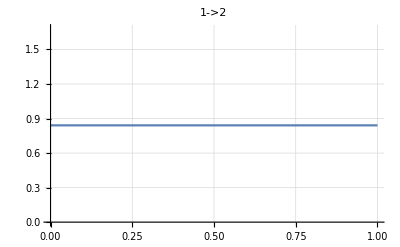
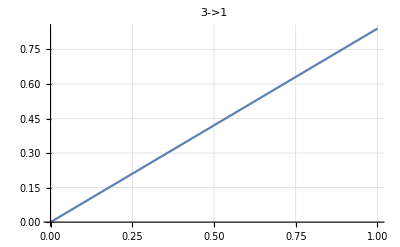
{-Graphics-,-Graphics-,-Graphics-}

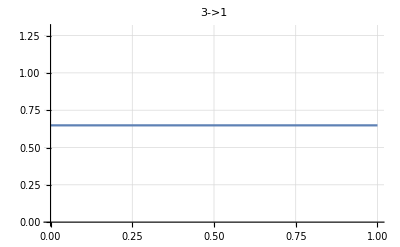
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
alpha[x_]:=1.4;
d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}];
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
plotUs[nn,"AssoNonCritical"]
plotMs[nn,"AssoNonCritical"]
```

```mathematica
alpha=1.77
```

Iterative DNF convertion took 0.018578 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,0.}
{0,0,-0.352037}

Iterative DNF convertion took 0.020135 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,-0.352037}
{0,0,-0.352037}

Iterative DNF convertion took 0.018533 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,-0.352037}
{0,0,-0.352037}

Iterated 3 times out of 15

{0.140607,Null}

All restrictions are True

Nlhs: {0.,0.,-0.352037}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,-0.352037}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 1.39364×10^-11

<|u1→0.647963,u2→0.647963,u3→0.,u4→0.,u5→0.,u6→0.647963,u7→0.,u8→0.,u9→0.647963,u10→0.647963,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

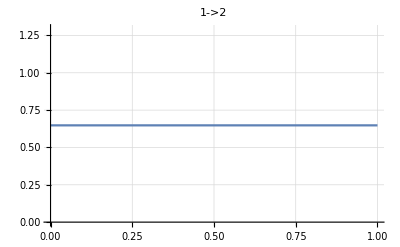
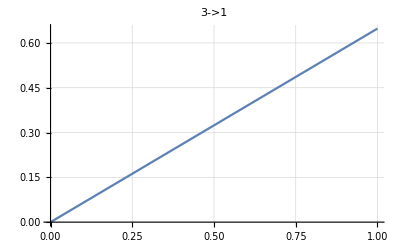
{-Graphics-,-Graphics-,-Graphics-}

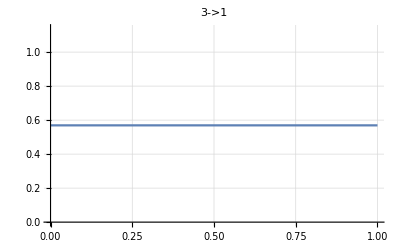
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
alpha[x_]:=1.77;
d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}];
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
plotUs[nn,"AssoNonCritical"]
plotMs[nn,"AssoNonCritical"]
```

```mathematica
alpha=1.8
```

Iterative DNF convertion took 0.019211 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,0.}
{0,0,-0.370039}

Iterative DNF convertion took 0.019572 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,-0.370039}
{0,0,-0.370039}

Iterative DNF convertion took 0.018448 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,-0.370039}
{0,0,-0.370039}

Iterated 3 times out of 15

{0.137743,Null}

All restrictions are True

Nlhs: {0.,0.,-0.370039}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,-0.370039}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 4.74372×10^-11

<|u1→0.629961,u2→0.629961,u3→0.,u4→0.,u5→0.,u6→0.629961,u7→0.,u8→0.,u9→0.629961,u10→0.629961,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

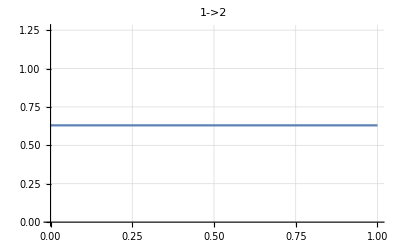
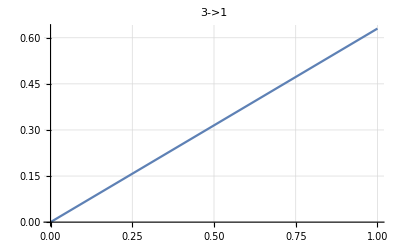
{-Graphics-,-Graphics-,-Graphics-}

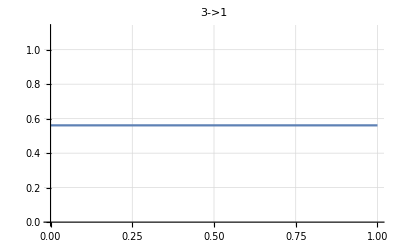
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
alpha[x_]:=1.8;
d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}];
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
plotUs[nn,"AssoNonCritical"]
plotMs[nn,"AssoNonCritical"]
```

```mathematica
alpha=1.9 works for I1=1,2 but not 4
```

Iterative DNF convertion took 0.012588 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,0.}
{0.302012,0.302012,0.513937}

Iterative DNF convertion took 0.015318 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.302012,0.302012,0.513937}
{0.479483,0.479483,-0.175055}

Iterative DNF convertion took 0.015014 seconds to terminate

Iterative DNF convertion took 2.×10^-6 seconds to terminate

{0.479483,0.479483,-0.175055}
{0.450575,0.450575,-0.0143633}

Iterative DNF convertion took 0.012284 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.450575,0.450575,-0.0143633}
{0.461919,0.461919,-0.0677765}

Iterative DNF convertion took 0.015832 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.461919,0.461919,-0.0677765}
{0.458752,0.458752,-0.0521944}

Iterative DNF convertion took 0.016764 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.458752,0.458752,-0.0521944}
{0.459725,0.459725,-0.0569174}

Iterative DNF convertion took 0.015075 seconds to terminate

Iterative DNF convertion took 2.×10^-6 seconds to terminate

{0.459725,0.459725,-0.0569174}
{0.459434,0.459434,-0.0555024}

Iterative DNF convertion took 0.018122 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.459434,0.459434,-0.0555024}
{0.459522,0.459522,-0.0559278}

Iterative DNF convertion took 0.014732 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.459522,0.459522,-0.0559278}
{0.459496,0.459496,-0.0558}

Iterative DNF convertion took 0.016307 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.459496,0.459496,-0.0558}
{0.459504,0.459504,-0.0558384}

Iterative DNF convertion took 0.015261 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.459504,0.459504,-0.0558384}
{0.459501,0.459501,-0.0558269}

Iterative DNF convertion took 0.015634 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.459501,0.459501,-0.0558269}
{0.459502,0.459502,-0.0558303}

Iterative DNF convertion took 0.013818 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.459502,0.459502,-0.0558303}
{0.459502,0.459502,-0.0558293}

Iterative DNF convertion took 0.017128 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.459502,0.459502,-0.0558293}
{0.459502,0.459502,-0.0558296}

Iterative DNF convertion took 0.017764 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.459502,0.459502,-0.0558296}
{0.459502,0.459502,-0.0558295}

Iterated 15 times out of 15

{1.28337,Null}

All restrictions are True

Nlhs: {0.459502,0.459502,-0.0558296}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.459502,0.459502,-0.0558295}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 9.39592×10^-8

<|u1→1.32311,u2→1.16156,u3→0.161556,u4→0.,u5→0.,u6→1.32311,u7→0.,u8→0.,u9→1.32311,u10→1.32311,j1→0.,j2→0.621058,j3→0.,j4→0.621058,j5→1.37894,j6→0.,j7→0.,j8→2.,j9→0.,j10→2.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.621058,jt6→1.37894,jt7→0.621058,jt8→0.,jt9→0.,jt10→0.621058,jt11→0.,jt12→1.37894,jt13→0.,jt14→0.|>

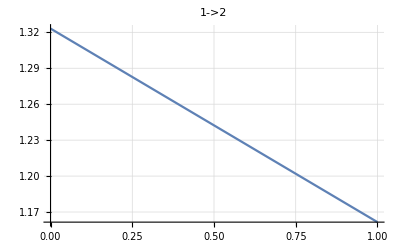
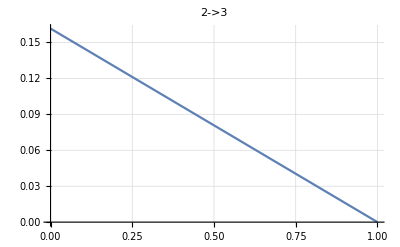
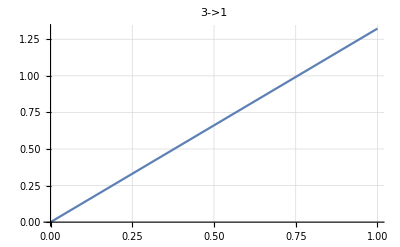

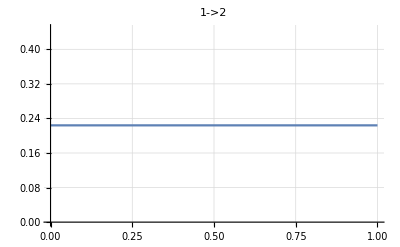
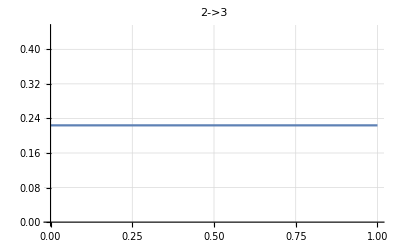
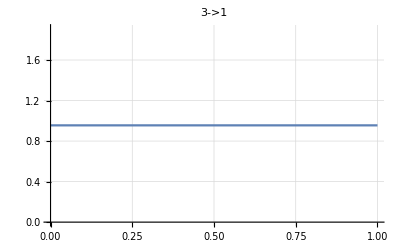

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
alpha[x_]:=1.9;
d2e=Data2Equations[Data/.{I1->2,U1->0,S1->1, S2->0}];
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
plotUs[nn,"AssoNonCritical"]
plotMs[nn,"AssoNonCritical"]
```

```mathematica
alpha=0.2
```

Iterative DNF convertion took 0.019555 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{0.,0.,-0.5}
{0,0,-0.5}

Iterative DNF convertion took 0.018429 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{0.,0.,-0.5}
{0,0,-0.5}

Iterated 2 times out of 15

{0.103887,Null}

All restrictions are True

Nlhs: {0.,0.,-0.5}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,-0.5}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 5.55112×10^-16

<|u1→0.5,u2→0.5,u3→0.,u4→0.,u5→0.,u6→0.5,u7→0.,u8→0.,u9→0.5,u10→0.5,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

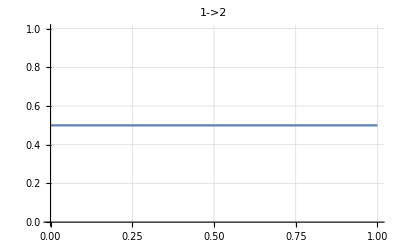
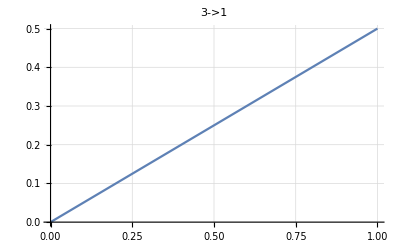
{-Graphics-,-Graphics-,-Graphics-}

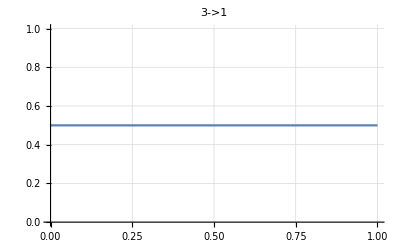
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
alpha[x_]:=2;
d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}];
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
plotUs[nn,"AssoNonCritical"]
plotMs[nn,"AssoNonCritical"]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,1,0},{0,0,1},{1,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>;
(crit=CriticalCongestionReduce[d2e=Data2Equations[Data/.{I1->1,U1->0,S1->1, S2->0}]];)//AbsoluteTiming
```

Reducing jt1≥0&&jt10≤1&&jt10≥0&&jt1≤jt10+jt3&&1/3+jt1≥jt10+jt3&&jt3≥0&&jt1≤999999+jt10+jt3+u1&&1+jt1≥jt10+jt3+u1&&u1≤1000000+u10&&u1≥u10&&(jt1==0||1/3+jt1==jt10+jt3)&&(jt10==1||1+jt1==jt10+jt3+u1)&&(jt10==0||1+jt1==jt10+jt3+u1)&&(jt10+jt3==0||jt1==jt10+jt3)&&(jt10+jt3==0||jt1==0)&&(1+jt1==jt10||jt3==0)&&(jt1==0||jt10+jt3==0)&&(jt1==0||jt10+jt3==0)&&(jt10==1||u1==u10)&&(jt10==0||u1==u10)&&(jt1==0||jt3==0)&&(jt1==0||jt3==0) ...

Part::partw: Part 1 of {} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{}⟦1⟧,Heading→].

Reduce took 0.263844 seconds to terminate

Reducing True ...

Reduce took 0.000055 seconds to terminate

Reducing True ...

Reduce took 0.000045 seconds to terminate

{0.323934,Null}

#### we may want to compare the performances of Reduce and ZAnd. do this after preprocessing. we may also want to compare the performances of the naive approach and ours. boolean convert from the start and reduce each disjunct.

```mathematica
IsNonLinearSolution[crit][crit["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {0.,0.,1.11022×10^-15}
{-j1+j2-Abs[IntM[-j1+j2,1->2]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->3]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->1]] Sign[-j5+j6]}

Max error for non-linear solution: 1.11022×10^-15

<|u1→1.,u2→1.,u3→0.,u4→0.,u5→0.,u6→1.,u7→0.,u8→0.,u9→1.,u10→1.,j1→0.,j2→0.,j3→0.,j4→0.,j5→1.,j6→0.,j7→0.,j8→1.,j9→0.,j10→1.,jt1→0.,jt2→0.,jt3→0.,jt4→0.,jt5→0.,jt6→1.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1.,jt13→0.,jt14→0.|>

## Non-critical congestion

```mathematica
Cost[current_,edge_]
```

Abs[IntM[current_,edge_]]

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

EliminateVarsSimplify for the us

Not finished with the us!

Reducing further (NewReduce)...

Simplifying...

Done!

<|u1→1,u2→1,u3→0,u4→0,u5→0,u6→1,u7→0,u8→0,u9→1,u10→1,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

<|u1→396850263/500000000,u2→396850263/500000000,u3→0,u4→0,u5→0,u6→396850263/500000000,u7→0,u8→0,u9→396850263/500000000,u10→396850263/500000000,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

<|u1→1/2,u2→1/2,u3→0,u4→0,u5→0,u6→1/2,u7→0,u8→0,u9→1/2,u10→1/2,j1→0,j2→0,j3→0,j4→0,j5→1,j6→0,j7→0,j8→1,j9→0,j10→1|>

### DataToEquations and the critical congestion solver

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→7.71442,u163→5.,u164→5.,u165→5,u166→7.71442,u167→7.71442,u168→5.,u169→7.71442,u170→5,u171→7.71442|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→7.96984,u163→5.,u164→5.,u165→5,u166→7.96984,u167→7.96984,u168→5.,u169→7.96984,u170→5,u171→7.96984|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→8.62682,u163→5.,u164→5.,u165→5,u166→8.62682,u167→8.62682,u168→5.,u169→8.62682,u170→5,u171→8.62682|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→13.3004,u163→5.,u164→5.,u165→5,u166→13.3004,u167→13.3004,u168→5.,u169→13.3004,u170→5,u171→13.3004|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.06581×10^-14,ComplexInfinity]

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→15,u163→5,u164→5,u165→5,u166→15,u167→15,u168→5,u169→15,u170→5,u171→15|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→0,j216→0,j217→10,j218→0,j219→0,jt220→0,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→10,jt232→0,jt233→0,u234→87.1921,u235→5.,u236→5.,u237→5,u238→87.1921,u239→87.1921,u240→5.,u241→87.1921,u242→5,u243→87.1921|>

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.890369

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.963772

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00707

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→1.41033×10^214,j216→1.41033×10^214,j217→1.41033×10^214,j218→0,j219→0,jt220→1.41033×10^214,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→1.41033×10^214,jt228→0,jt229→0,jt230→1.41033×10^214,jt231→10,jt232→0,jt233→0,u234→0,u235→0.,u236→5.,u237→5,u238→0.,u239→0.,u240→5.,u241→0.,u242→5,u243→0.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j138→0,j139→0,j140→0,j141→10,j142→10,j143→0,j144→0,j145→10,j146→0,j147→0,jt148→0,jt149→0,jt150→0,jt151→0,jt152→0,jt153→10,jt154→0,jt155→0,jt156→0,jt157→0,jt158→0,jt159→10,jt160→0,jt161→0,u162→140.721,u163→5.,u164→5.,u165→5,u166→140.721,u167→140.721,u168→5.,u169→140.721,u170→5,u171→140.721|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00359

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2),(√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2))/(√(2 Abs[-1.42247815737932×10^354+0. j211+0. j216]^2+Abs[-1.42247815737932×10^354+0. j211+0. j216+0. u234]^2)),(√(Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[-10+j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216-IntM[j211-j216]]^2+Abs[-1.42247815737932×10^354-1. j211+1. j216+0. u234-IntM[j211-j216]]^2))/(√(Abs[-10+j211-j216+IntM[-10+j211-j216]]^2+2 Abs[j211-j216+IntM[j211-j216]]^2))]

ReplaceAll::reps: {u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216] is not a list, Rule, or Association.

ReplaceAll::reps: {u236==5&&u238==u241&&u240==5&&j211-j216-u234+u239==j211-j216+IntM[j211-j216]&&j211-j216-u235+u240==j211-j216+IntM[j211-j216]&&-10+j211-j216-u236+u241==-10+j211-j216+IntM[-10+j211-j216]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j210→0,j211→0,j212→0,j213→10,j214→10,j215→0,j216→0,j217→10,j218→0,j219→0,jt220→0,jt221→0,jt222→0,jt223→0,jt224→0,jt225→10,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→10,jt232→0,jt233→0,u234→15,u235→5,u236→5,u237→5,u238→15,u239→15,u240→5,u241→15,u242→5,u243→15|>